## Stability diagram plot

```mathematica
ClearAll["Global`*"];
```

### Defenitions

```mathematica
Clear[κ,α,Qp,Qm,γ,γd,γp,γa,a,μ];
Eq1=-Sqrt[(Qm/Qp)] (Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));
Eq2=Sqrt[Qp/Qm] (-Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));

Eq3=a (Sqrt[Qm/Qp]+Sqrt[Qp/Qm]) γa+(-Sqrt[((Qm-a^2 Qm)/Qp)]+Sqrt[(Qp-a^2 Qp)/Qm]) γp+(2 (Qm-Qp) α γ κ μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd);

Ns=((Qm γ+Qp γ+γd) μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);

ns=((Qm-Qp) γ μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);

ω=Sqrt[Qp/Qm] ((α γa-γp) Cos[2 ψ]-(γa+α γp) Sin[2 ψ]);

M={{-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),-Sqrt[(Qm/Qp)] (-a γa+Sqrt[1-a^2] γp),-Sqrt[1-a^2] γa-a γp,-a γa+Sqrt[1-a^2] γp,Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (-a γa+Sqrt[1-a^2] γp),-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa-a γp,Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-Sqrt[1-a^2] γa+a γp,a γa+Sqrt[1-a^2] γp,-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qp/Qm] (-a γa-Sqrt[1-a^2] γp),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa+a γp,-Sqrt[(Qp/Qm)] (-a γa-Sqrt[1-a^2] γp),-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};
(*M={{-Sqrt[(Qm/Qp)] (-γa Cos[2 ψ]-γp Sin[2 ψ]),-Sqrt[(Qm/Qp)] (γp Cos[2 ψ]-γa Sin[2 ψ]),-γa Cos[2 ψ]-γp Sin[2 ψ],γp Cos[2 ψ]-γa Sin[2 ψ],Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (γp Cos[2 ψ]-γa Sin[2 ψ]),-Sqrt[(Qm/Qp)] (-γa Cos[2 ψ]-γp Sin[2 ψ]),-γp Cos[2 ψ]+γa Sin[2 ψ],-γa Cos[2 ψ]-γp Sin[2 ψ],Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-γa Cos[2 ψ]+γp Sin[2 ψ],γp Cos[2 ψ]+γa Sin[2 ψ],-Sqrt[(Qp/Qm)] (-γa Cos[2 ψ]+γp Sin[2 ψ]),Sqrt[Qp/Qm] (-γp Cos[2 ψ]-γa Sin[2 ψ]),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-γp Cos[2 ψ]-γa Sin[2 ψ],-γa Cos[2 ψ]+γp Sin[2 ψ],-Sqrt[(Qp/Qm)] (-γp Cos[2 ψ]-γa Sin[2 ψ]),-Sqrt[(Qp/Qm)] (-γa Cos[2 ψ]+γp Sin[2 ψ]),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};*)
```

```mathematica
MR={{2(γa+I γp),0,2Sqrt[Q] (1+I α)κ},{0,2(γa-I γp),2Sqrt[Q] (1-I α)κ},{-γ/κ Sqrt[Q] (κ+γa),-γ/κ Sqrt[Q] (κ+γa),-(γd+2γ Q)}};
Coefs=CoefficientList[CharacteristicPolynomial[MR,λ],λ]*(-1)/.{Q-> 1/2(κ μ/(κ+γa)-1)}//FullSimplify;
```

```mathematica
line1=μ/.Solve[Coefs[[3]]==0,μ][[1]]//FullSimplify;
line2=μ/.Solve[Coefs[[2]]==0,μ][[1]]//FullSimplify;
line3=μ/.Solve[Coefs[[1]]==0,μ][[1]]//FullSimplify;
lineΔ1=μ/.Solve[Coefs[[3]]*Coefs[[2]]-Coefs[[1]]==0,μ][[1]]//FullSimplify;
lineΔ2=μ/.Solve[Coefs[[3]]*Coefs[[2]]-Coefs[[1]]==0,μ][[2]]//FullSimplify;
```

#### Tests:

```mathematica
Coefs
```

{4 (γa^2 γd+γ γa (α γp+κ)+γp (-γ γp+γd γp+α γ κ)-(γ κ (-γp^2+γa κ+α γp (γa+κ)) μ)/(γa+κ)),4 (γa^2-γa γd+γp^2)+(2 γ (γa-κ) (γa+κ-κ μ))/(γa+κ),-4 γa+γd+γ (-1+(κ μ)/(γa+κ)),1}

```mathematica
M.{0,Sqrt[Qp],0,Sqrt[Qm],0,0}//FullSimplify[#,Assumptions-> {Qp>0&&Qm>0}]&
```

{0,0,0,0,0,0}

```mathematica
M//FullSimplify[#,Assumptions-> {Qp>0&&Qm>0}]&//MatrixForm
```

(√(Qm/Qp) (√(1-a^2) γa+a γp) | √(Qm/Qp) (a γa-√(1-a^2) γp) | -√(1-a^2) γa-a γp | -a γa+√(1-a^2) γp | √Qp κ | √Qp κ
√(Qm/Qp) (-a γa+√(1-a^2) γp) | √(Qm/Qp) (√(1-a^2) γa+a γp) | a γa-√(1-a^2) γp | -√(1-a^2) γa-a γp | √Qp α κ | √Qp α κ
-√(1-a^2) γa+a γp | a γa+√(1-a^2) γp | √(Qp/Qm) (√(1-a^2) γa-a γp) | -√(Qp/Qm) (a γa+√(1-a^2) γp) | √Qm κ | -√Qm κ
-a γa-√(1-a^2) γp | -√(1-a^2) γa+a γp | √(Qp/Qm) (a γa+√(1-a^2) γp) | √(Qp/Qm) (√(1-a^2) γa-a γp) | √Qm α κ | -√Qm α κ
-(2 √Qp γ (2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) | 0 | -(2 √Qm γ (2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) | 0 | -(1+Qm+Qp) γ | (Qm-Qp) γ
-(2 √Qp γ (2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) | 0 | (2 √Qm γ (2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) | 0 | (Qm-Qp) γ | -(Qm+Qp) γ-γd)

### For gradient method

```mathematica
avars={a5,a4,a3,a2,a1};
vars={Qp,Qm,ψ};
params={Λ,γp};
charpolycoefs={-2 Qm Qp γ (γa^2+γp^2) Cos[2 ψ] ((Sqrt[Qm^3 Qp]-Sqrt[Qm Qp^3]) (γ γa-α γd γp)+(Qm-Qp) (Qp (γ+γd)+Qm (γ+4 Qp γ+γd)) κ Cos[2 ψ]+(Qm-Qp) Sqrt[Qm Qp] (γ γa+α γd γp) Cos[4 ψ]+α ((Qm+Qp) (Qm+Qp+4 Qm Qp) γ+(Qm-Qp)^2 γd) κ Sin[2 ψ]+Qm Sqrt[Qm Qp] α γ γa Sin[4 ψ]+Qp Sqrt[Qm Qp] α γ γa Sin[4 ψ]+4 (Qm Qp)^(3/2) α γ γa Sin[4 ψ]-4 (Qm Qp)^(3/2) γ γp Sin[4 ψ]-Qm Sqrt[Qm Qp] γd γp Sin[4 ψ]-Qp Sqrt[Qm Qp] γd γp Sin[4 ψ]),γ (-2 (Qm-Qp) (Qm Qp)^(3/2) γa (γa^2+γp^2) Cos[2 ψ]^3+2 (α γa+γp) Sin[2 ψ] ((4 Qm (Qm Qp)^(3/2) γ+2 (Qm Qp)^(3/2) (γ+2 Qp γ-γd)+(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) (γ+γd)) κ+2 Qm Qp (-Qm+Qp) γd γp Sin[2 ψ])+2 Qm Cos[2 ψ]^2 (2 Qp (γa^2 (2 (Qm-Qp) γ+(1+Qm+Qp) γd)-(Qm+Qp+4 Qm Qp) α γ γa γp+((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd) γp^2)+Qp (-Qm+Qp) (Qm+Qp) (γa^2+γp^2) κ-((Qm Qp)^(3/2)+Sqrt[Qm Qp^5]) (α γa-γp) (γa^2+γp^2) Sin[2 ψ])+Cos[2 ψ] (8 Qm (Qm Qp)^(3/2) γ (γa-α γp) κ+2 (γ+γd) ((Sqrt[Qm^5 Qp]-3 Sqrt[Qm Qp^5]) γa-(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) α γp) κ-(Qm Qp)^(3/2) (Qp α γp (γa^2+γp^2)+4 (γ-γd) (γa+α γp) κ+8 Qp γ (3 γa+α γp) κ)+Qm Qp (Qp Sqrt[Qm Qp] α γp (γa^2+γp^2) Cos[4 ψ]+2 Sin[2 ψ] (2 ((Qm+Qp+4 Qm Qp) α γ γa^2+γa (Qp (γ-3 γd)+Qm (γ-4 Qp γ-γd)) γp+(Qm-Qp) α γd γp^2)-(Qm^2+Qp^2) α (γa^2+γp^2) κ+Qm Sqrt[Qm Qp] α γp (γa^2+γp^2) Sin[2 ψ])))),Qm Qp (γa^2 (γ+3 Qm γ-Qp γ+γd)-2 Qm α γ γa γp+((1+Qm+3 Qp) γ+γd) γp^2)+4 Qp γ (Qm (γ+4 Qp γ-γd)+Qp (γ+γd)) κ-2 γ (8 (Qm Qp)^(3/2) γ γa+4 Sqrt[Qm^3 Qp] γ γa+4 Sqrt[Qm Qp] γa γd+4 Sqrt[Qm^3 Qp] γa γd+4 Sqrt[Qm Qp^3] γa γd-Sqrt[Qm^5 Qp] γa κ+3 Sqrt[Qm Qp^5] γa κ+Sqrt[Qm^5 Qp] α γp κ+Sqrt[Qm Qp^5] α γp κ) Cos[2 ψ]+Qm Qp (γa^2 (γ+3 Qm γ-Qp γ+γd)-2 Qp α γ γa γp+((1+3 Qm+Qp) γ+γd) γp^2) Cos[4 ψ]+γ (2 (8 (Qm Qp)^(3/2) γ γp+4 Sqrt[Qm Qp^3] γd γp+(Sqrt[Qm^5 Qp]+Sqrt[Qm Qp^5]) (α γa+γp) κ) Sin[2 ψ]+Qm Qp ((Qm+Qp) α γa^2-2 Qp γa γp+(Qm-Qp) α γp^2) Sin[4 ψ]),-4 γa ((Sqrt[Qm Qp]+2 Sqrt[Qm^3 Qp]+Sqrt[Qm Qp^3]) γ+Sqrt[Qm Qp] γd) Cos[2 ψ]+Qm Qp (γa^2+γp^2) Cos[2 ψ]^2+4 γ (γd+Qm (γ+4 Qp γ+γd)+Qp (γ+γd+Qp κ)+Sqrt[Qm Qp^3] γp Sin[2 ψ]),2 (γ+2 Qm γ+2 Qp γ+γd-Sqrt[Qm Qp] γa Cos[2 ψ]),1};
charpolycoefs=charpolycoefs[[1;;5]];
stateqns={
κ(Ns+ns - 1)-γa Sqrt[Qm/Qp] Cos[2 ψ]- γp Sqrt[Qm/Qp]Sin[2 ψ], κ  α(Ns+ns - 1)+γa Sqrt[Qm/Qp] Sin[2 ψ]-γp Sqrt[Qm/Qp]Cos[2 ψ]-ω,κ (Ns-ns- 1)-γa Sqrt[Qp/Qm]Cos[2 ψ]+ γp Sqrt[Qp/Qm] Sin[2 ψ],κ  α(Ns-ns - 1)-γa Sqrt[Qp/Qm]Sin[2 ψ]-γp Sqrt[Qp/Qm]Cos[2 ψ]-ω,-γ(Ns -Λ)-γ(Ns+ns) Qp-γ(Ns-ns) Qm,-γd ns-γ(Ns+ns) Qp+γ(Ns-ns) Qm};
stateqns[[2]]=stateqns[[2]]-stateqns[[4]]//FullSimplify;
stateqns=Drop[stateqns,{4}];
HwM={
{a1,a3,a5,0},
{1,a2,a4,0},
{0,a1,a3,a5},
{0,1,a2,a4}};
dDda=Table[D[Det[HwM],avars[[i]]],{i,1,5}];
dadx=Table[D[charpolycoefs[[i]],vars[[j]]],{i,1,5},{j,1,3}];
dadp=Table[D[charpolycoefs[[i]],params[[j]]],{i,1,5},{j,1,2}];
solNn = Solve[stateqns[[4;;5]]==0,vars[[4;;5]]][[1]]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&ψ∈Reals}]&;
stat3eqns = stateqns[[1;;3]]/.solNn//FullSimplify[#,Assumptions->{Qp>0&&Qm>0&&ψ∈Reals}]&;
dfdx=Table[D[stat3eqns[[i]],vars[[j]]],{i,1,3},{j,1,3}]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&;
dfdp=Table[D[stat3eqns[[i]],params[[j]]],{i,1,3},{j,1,2}]//FullSimplify[#,Assumptions->{Qp>0&&Qm>0}]&;
```

Part::take: Cannot take positions 4 through 5 in {Qp,Qm,ψ}.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partw: Part 3 of {κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])-√(Qm/Qp) (γa Cos[Times[«2»]]+γp Sin[Times[«2»]]),(2 (Qm-Qp) α γ κ μ)/(Plus[«3»] γ+Plus[«3»] γd)+(-√Times[«2»]+√(Power[«2»] Qp)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)),κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])+√(Qp/Qm) (-γa Cos[Times[«2»]]+γp Sin[Times[«2»]])}/.{}⟦1⟧ does not exist.

Part::pkspec1: The expression #2 cannot be used as a part specification.

Part::partw: Part 3 of {κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])-√(Qm/Qp) (γa Cos[Times[«2»]]+γp Sin[Times[«2»]]),(2 (Qm-Qp) α γ κ μ)/(Plus[«3»] γ+Plus[«3»] γd)+(-√Times[«2»]+√(Power[«2»] Qp)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)),κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])+√(Qp/Qm) (-γa Cos[Times[«2»]]+γp Sin[Times[«2»]])}/.{}⟦1⟧ does not exist.

Part::pkspec1: The expression #2 cannot be used as a part specification.

Part::partw: Part 3 of {κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])-√(Qm/Qp) (γa Cos[Times[«2»]]+γp Sin[Times[«2»]]),(2 (Qm-Qp) α γ κ μ)/(Plus[«3»] γ+Plus[«3»] γd)+(-√Times[«2»]+√(Power[«2»] Qp)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)),κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])+√(Qp/Qm) (-γa Cos[Times[«2»]]+γp Sin[Times[«2»]])}/.{}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression #2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$Aborted

Part::partw: Part 3 of {κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])-√(Qm/Qp) (γa Cos[Times[«2»]]+γp Sin[Times[«2»]]),(2 (Qm-Qp) α γ κ μ)/(Plus[«3»] γ+Plus[«3»] γd)+(-√Times[«2»]+√(Power[«2»] Qp)) γp Cos[2 ψ]+((Qm+Qp) γa Sin[2 ψ])/(√(Qm Qp)),κ (-1+((Times[«3»]+γd) μ)/Plus[«3»])+√(Qp/Qm) (-γa Cos[Times[«2»]]+γp Sin[Times[«2»]])}/.{}⟦1⟧ does not exist.

Part::pkspec1: The expression #2 cannot be used as a part specification.

### Solution

```mathematica
(*Solving stationary problem*)
	
γa=0.1;
γ=1.;
κ=300.;
γd=50.;
α=5.;
γp=2π*1.9810933606070646;
μ=(Nth*1.0000505082608369-Ntr)/(Nth-Ntr);
μ=(Nth*1.0000605082608369-Ntr)/(Nth-Ntr);
Qp0=0.9;
Qm0=0.1;
a0=-0.1;
Nth=6.25*10^6;
Ntr=5.935*10^6;

Qm0v2=1/2 (-1-Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2]/(2 γ (γa+α γp) κ)+μ);
Qp0v2=1/2 (-1+Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2]/(2 γ (γa+α γp) κ)+μ);
tan0v2=((α γa-γp) Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2])/(2 γ (γa+α γp)^2 κ (-1+μ));
a0v2=tan0v2/Sqrt[1+tan0v2^2];
If[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2<0.3*(2 γ (γa+α γp) κ),Qm0v2=(μ-1)/2;Qp0v2=(μ-1)/2;a0v2=0;]
(*Qm0v2=(μ-1)/2*0.1;Qp0v2=(μ-1)/2*0.9;a0v2=0;*)
(*Nsol=NSolve[{Eq1==0,Eq2==0,Eq3==0},{Qp,Qm,a}]//Select[#,AllTrue[{Qp,Qm,a}/.#,#∈Reals&]&]&;*)
(*If[Length[Nsol]==0,Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}],
ElSol=Select[Nsol,(Abs[Qp-Qm]/.#)>10^-6&];
If[Length[ElSol]==0,Nsol=Nsol[[1]],Nsol=ElSol[[1]]]
];*)
(*β=((α γa-γp)-(γa+α γp) a0)/((α γa-γp) +(γa+α γp) a0);
Qp0=(μ-1)/(1+β);
Qm0=β Qp0;*)
Nsol2=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0v2,N[10^-8],10.},{Qm,Qm0v2,N[10^-8],10.},{a,a0v2,-1.,1.}}]
(*Nsol=Flatten[{Nsol,ψ-> ArcSin[a/.Nsol]/2}];*)
(*Ns-1/.Nsol
ns/.Nsol
Nsol*)
```

{Qp→0.000433469,Qm→0.000433469,a→0.}

```mathematica
μ+(Nth*0.00001/(Nth-Ntr))
```

1.0012

```mathematica
μ
```

1.0012

```mathematica
CheckStability[κ,α,γ,γd,γp,γa,μ,Qp0,Qm0,a0]
```

{0,16092.,31265.3,31552.8,650.493,50.6017,1}

{1363.31,-1.12167×10^12}

{0,{Qp→0.000433469,Qm→0.000433469,a→1.61×10^-15}}

```mathematica
lineΔ2
```

1.01219

```mathematica
{Eq1,Eq2,Eq3}/.Nsol2
```

{1.22208×10^-13,1.22208×10^-13,-5.39002×10^-18}

```mathematica
(*Evaluating charpoly*)

p=CoefficientList[CharacteristicPolynomial[M/.Nsol2,λ],λ];
p[[1]]=0;
(*p=-CoefficientList[CharacteristicPolynomial[(tmp2/.Nsol),λ],λ];*)
Dets=ConstantArray[0,2];
Dets[[1]]=p[[4]]*p[[5]]-p[[3]]; (*D2*)
Dets[[2]]=Det[{
{p[[6]],p[[4]],p[[2]],0},
{1,p[[5]],p[[3]],0},
{0,p[[6]],p[[4]],p[[2]]},
{0,1,p[[5]],p[[3]]}}];(*D4*)
If[AllTrue[p[[2;;]],Positive],
If[AllTrue[Dets,Positive],
Print["System is stable"];
Print[p//MatrixForm];
Print[Dets//MatrixForm],
Print["Some Hurwitz determinants are negative:"];
Print[p//MatrixForm];
Print[Dets//MatrixForm]
],
Print["Some p < 0"];
Print[p//MatrixForm];
Print[Dets//MatrixForm];
]
```

Some Hurwitz determinants are negative:

(0
12416.2
31202.4
31561.3
650.245
50.6013
1)

(2.04914×10^7
-1.14314×10^12)

```mathematica
p
```

{0,12416.2,31202.4,31561.3,650.245,50.6013,1}

```mathematica
CheckStability[κ,α,γ,γd,γp,γa,μ,Qp0,Qm0,a0]
```

{0,12416.2,31202.4,31561.3,650.245,50.6013,1}

{1341.92,-1.14314×10^12}

{0,{Qp→0.000334296,Qm→0.000334296,a→-5.33188×10^-16}}

```mathematica
ShowImageWithTicks[img_,xRange_,yRange_]:=Module[{dims=ImageDimensions[img]},Show[img,Frame->True,FrameTicks->{{Partition[Riffle[Range[0,dims[[2]],dims[[2]]/(Length[yRange]-1)],yRange],2],None},{Partition[Riffle[Range[0,dims[[1]],dims[[1]]/(Length[xRange]-1)],xRange],2],None}}]]
```

### Plotting by pixels v0

```mathematica
γa=-0.01;
γ=1.;
γp=10;
κ=300.;
γd=50.;
α=3.;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;
ysub={Sqrt[1-a^2]-> -Sqrt[1-a^2]};
Nμ=100;
Nγp=100;
μs=CoordinateBoundsArray[{{1.,5.}},Into[Nμ]]//Flatten;
γps=CoordinateBoundsArray[{{1.,2.}},Into[Nγp]]//Flatten//Power[10,#]&;
result=ConstantArray[0,{Nγp,Nμ}];
result2=ConstantArray[0,{Nγp,Nμ}];
For[i=1,i<= Nμ,i++,
For[j=1,j<= Nγp,j++,
μ=μs[[i]];
γp=γps[[j]];

Nsol=FindRoot[({Eq1,Eq2,Eq3})==0,{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
p=CoefficientList[CharacteristicPolynomial[M/.Nsol,λ],λ];
p[[1]]=0;
If[AllTrue[p[[2;;]],Positive],
	Dets=ConstantArray[0,2];
Dets[[1]]=p[[6]]*p[[5]]-p[[4]]; (*D2*)
Dets[[2]]=Det[{
{p[[6]],p[[4]],p[[2]],0},
{1,p[[5]],p[[3]],0},
{0,p[[6]],p[[4]],p[[2]]},
{0,1,p[[5]],p[[3]]}}];(*D4*)

If[AllTrue[Dets,Positive],
If[Abs[Qp-Qm/.Nsol]<10^-8,result[[i,j]]=1,result[[i,j]]=0.7],
result[[i,j]]=0;
]
(*result[[i,j]]=0;
If[Dets[[1]]>0,result[[i,j]]=0.3,];
If[Dets[[2]]>0,result[[i,j]]=result[[i,j]]+0.7,] ***=> D4 fails****)
,
result[[i,j]]=0;
];
Dets=ConstantArray[0,5];
HurwM={
{p[[6]],p[[4]],p[[2]],0,0},
{1,p[[5]],p[[3]],0,0},
{0,p[[6]],p[[4]],p[[2]],0},
{0,1,p[[5]],p[[3]],0},
{0,0,p[[6]],p[[4]],p[[2]]}};
Dets[[1]]=HurwM[[1,1]];
Dets[[2]]=Det[HurwM[[1;;2,1;;2]]];
Dets[[3]]=Det[HurwM[[1;;3,1;;3]]];
Dets[[4]]=Det[HurwM[[1;;4,1;;4]]];
Dets[[5]]=Det[HurwM[[1;;5,1;;5]]];
If[AllTrue[Dets,Positive],
If[Abs[Qp-Qm/.Nsol]<10^-8,result2[[i,j]]=1,result2[[i,j]]=0.7],
result2[[i,j]]=0;
];
If[Not[AllTrue[({Eq1,Eq2,Eq3}/.Nsol//Chop)==  0]],result[[i,j]]=-1]
]
];
Image[Reverse[result]]
Image[Reverse[result2]]
Image[Reverse[Abs[result2-result]]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

```mathematica
Select[Abs[result2-result]//Flatten,#≠  0&]
```

{}

```mathematica
Select[result//Flatten,#==-1&]
```

{}

```mathematica
newres=Table[If[result[[i,j]]>0.5,1,0],{i,1,Nμ},{j,1,Nγp}];
contour=Abs[newres[[2;;,2;;]]-newres[[;;-2,2;;]]]+Abs[newres[[2;;,2;;]]-newres[[2;;,;;-2]]];
rgb=ConstantArray[0,{Nμ,Nγp,3}];
rgb[[;;,;;,2]]=newres;
rgb[[2;;,2;;,1]]=contour;
Image[Reverse[rgb]]
```

-Graphics-

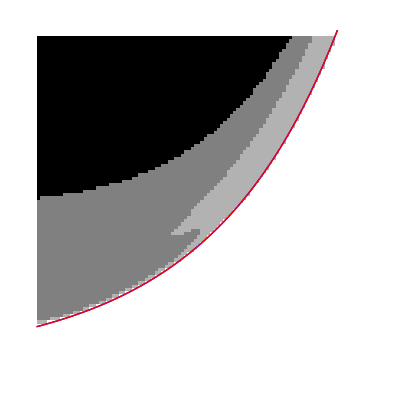

```mathematica
ap=ArrayPlot[1-Reverse[result]];
Mu[γp_]:=(κ+γa)*(α *γ *κ+α *γ *γa-γ *γp+γp *γd)/(γ *κ *(α *κ+α *γa-γp));
MuMine[γp_]:=((γa+κ) (γa^2 γd+γ γa (α γp+κ)+γp (-γ γp+γd γp+α γ κ)))/(γ κ (-γp^2+γa κ+α γp (γa+κ)));
Diff[γp_]:=(MuMine[γp]-Mu[γp])/MuMine[γp];

lp=Plot[(Mu[10*10^(x/Nγp)]-1)/5*Nμ,{x,0,Nγp},PlotStyle-> {Red,Thick}];
lmp=Plot[(MuMine[10*10^(x/Nγp)]-1)/5*Nμ,{x,0,Nγp},PlotStyle-> {Blue,Thick}];
Show[ap,lmp,lp,PlotRange-> {{0,Nγp},{0,Nμ}}]
```

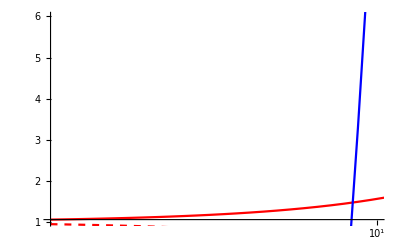

```mathematica
pl1 = Plot[1+γd*x/(γ (α κ - x)),{x,1,100},PlotStyle->Red,ScalingFunctions-> {"Log10",None}];
pl2 =Plot[1-γd/γ+2α x/γ,{x,1,100},PlotStyle->Blue,ScalingFunctions-> {"Log10",None}];
pl3 = Plot[1-γd*x/(γ (α κ + x)),{x,1,100},PlotStyle->{Red,Dashed},ScalingFunctions-> {"Log10",None}];
pl4 =Plot[1-γd/γ-2α x/γ,{x,1,100},PlotStyle->{Blue,Dashed},ScalingFunctions-> {"Log10",None}];
Show[pl1,pl2,pl3,pl4,PlotRange->{{0,1},{1,6}}]
```

```mathematica
oldresult=result;
```

### Plotting bound

```mathematica
Clear["Global`*"]
```

```mathematica
Clear[κ,α,γ,γa,γp,γd,μ,Qp0,Qm0,a0,Eq1,Eq2,Eq3,M,Dets,Nsol,ElSol, Ns, ns,p,Qp0v2,Qm0v2,a0v2,tan0v2];
CheckStability[κ_,α_,γ_,γd_,γp_,γa_,μ_,Qp0_,Qm0_,a0_]:=Module[{Eq1,Eq2,Eq3,M,Dets,Nsol,ElSol, Ns, ns,p,Qp0v2,Qm0v2,a0v2,tan0v2},

Eq1=-Sqrt[(Qm/Qp)] (Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));
Eq2=Sqrt[Qp/Qm] (-Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));

Eq3=a (Sqrt[Qm/Qp]+Sqrt[Qp/Qm]) γa+(-Sqrt[((Qm-a^2 Qm)/Qp)]+Sqrt[(Qp-a^2 Qp)/Qm]) γp+(2 (Qm-Qp) α γ κ μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd);
Ns=((Qm γ+Qp γ+γd) μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);ns=((Qm-Qp) γ μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);

M={{-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),-Sqrt[(Qm/Qp)] (-a γa+Sqrt[1-a^2] γp),-Sqrt[1-a^2] γa-a γp,-a γa+Sqrt[1-a^2] γp,Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (-a γa+Sqrt[1-a^2] γp),-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa-a γp,Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-Sqrt[1-a^2] γa+a γp,a γa+Sqrt[1-a^2] γp,-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qp/Qm] (-a γa-Sqrt[1-a^2] γp),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa+a γp,-Sqrt[(Qp/Qm)] (-a γa-Sqrt[1-a^2] γp),-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};

Qm0v2=1/2 (-1-Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2]/(2 γ (γa+α γp) κ)+μ);
Qp0v2=1/2 (-1+Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2]/(2 γ (γa+α γp) κ)+μ);
If[μ>1,
tan0v2=((α γa-γp) Sqrt[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2])/(2 γ (γa+α γp)^2 κ (-1+μ)),
tan0v2=0];
a0v2=tan0v2/Sqrt[1+tan0v2^2];

(*Print[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2];*)
If[-4 γd^2 (γa^2+γp^2)^2+4 γ^2 (γa+α γp)^2 κ^2 (-1+μ)^2<0.3*(2 γ (γa+α γp) κ),Qm0v2=(μ-1)/2*0.7;Qp0v2=(μ-1)/2*1.3;a0v2=-0.1;];
If[Qm0v2==0,Qm0v2=10^-7];
If[Qp0v2==0,Qp0v2=10^-7];
Nsol=FindRoot[({Eq1,Eq2,Eq3})==0,{{Qp,Qp0v2,N[10^-8],100.},{Qm,Qm0v2,N[10^-8],100.},{a,a0v2,-1.,1.}}];

If[Not[AllTrue[{Eq1,Eq2,Eq3}/.Nsol//Chop,#==0&]],Return[{-1,Nsol},Module]];
(*Nsol=NSolve[{Eq1==0,Eq2==0,Eq3==0},{Qp,Qm,a}]//Select[#,AllTrue[{Qp,Qm,a}/.#,#∈Reals&]&]&;
If[Length[Nsol]==0,Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}],
ElSol=Select[Nsol,(Abs[Qp-Qm]/.#)>10^-6&];
If[Length[ElSol]==0,Nsol=Nsol[[1]],Nsol=ElSol[[1]]]
];*)


p=CoefficientList[CharacteristicPolynomial[M/.Nsol,λ],λ];
p[[1]]=0;

If[AllTrue[p[[2;;]],Positive],
	Dets=ConstantArray[0,2];
Dets[[1]]=p[[6]]*p[[5]]-p[[4]]; (*D2*)
Dets[[2]]=Det[{
{p[[6]],p[[4]],p[[2]],0},
{1,p[[5]],p[[3]],0},
{0,p[[6]],p[[4]],p[[2]]},
{0,1,p[[5]],p[[3]]}}];(*D4*)

	If[AllTrue[Dets,Positive],
{1,Nsol},
{0,Nsol}],
{0,Nsol}
]
];
```

```mathematica
γa=-0.1;
γ=1.;
κ=300.;
γd=1500.;
α=5.;
Nth=6.25*10^6;
Ntr=5.935*10^6;

γd=200.;

γp=2*π*32;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;

(*Initial grid test*)
Nμ=50;
Nγp=50;
Nγd=50;
(*μmin=(1.*Nth-Ntr)/(Nth-Ntr);
μmax=(1.0045*Nth-Ntr)/(Nth-Ntr);
γpmin=2π*0.001;
γpmax=2π*0.04;*)
μmin=(1.*Nth-Ntr)/(Nth-Ntr);
μmax=(5.*Nth-Ntr)/(Nth-Ntr);
γpmin=2π*0.01;
γpmax=2π*100;
γdmin=1;
γdmax=20000;
accuracy=1.*^-5;
```

```mathematica
μs=CoordinateBoundsArray[{{μmin,μmax}},Into[Nμ]]//Flatten;
γds=CoordinateBoundsArray[{{Log10[γdmin],Log10[γdmax]}},Into[Nγd]]//Flatten//Power[10,#]&;
result=ConstantArray[0,{Nμ,Nγd}];
resulty=ConstantArray[0,{Nμ,Nγd}];
MuX[γdd_]:=((γa+κ) (γa^2 γdd+γ γa (α γp+κ)+γp (-γ γp+γdd γp+α γ κ)))/(γ κ (-γp^2+γa κ+α γp(γa+κ)));
t1=AbsoluteTime[];
For[i=1,i<= Nμ,i++,
For[j=1,j<= Nγd,j++,
(*If[μs[[i]]<MuX[γps[[j]]],result[[i,j]]=1,*)
res=CheckStability[κ,α,γ,γds[[j]],γp,γa,μs[[i]],Qp0,Qm0,a0];
result[[i,j]]=res[[1]];
res=CheckStability[κ,α,γ,γds[[j]],-γp,-γa,μs[[i]],Qp0,Qm0,a0];
resulty[[i,j]]=res[[1]];
(*Qp0=Qp/.res[[2]];Qm0=Qm/.res[[2]];a0=a/.res[[2]];*)
(*If[(Abs[Qp-Qm]/.res[[2]])<10^-8,result[[i,j]]=result[[i,j]]*0.5];*)
If[Not[AllTrue[({Eq1,Eq2,Eq3}/.res[[2]]//Chop)==  0]],result[[i,j]]=-1];(*];*)
]];
Print[AbsoluteTime[]-t1];
If[Length[Select[result//Flatten,#<0&]]>0,Print["Somewhere stationary equations were not properly solved!"]];
```

FindRoot::reged: The point {1.×10^-8,1.×10^-8,-0.0999463} is at the edge of the search region {1.×10^-8,100.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {1.×10^-8,1.×10^-8,-0.0999463} is at the edge of the search region {1.×10^-8,100.} in coordinate 2 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

16.320173

```mathematica
Image[Reverse[result]]
Image[Reverse[resulty]]
```

-Graphics-

-Graphics-

```mathematica
CheckStability[κ,α,γ,1500,γp,γa,150,Qp0,Qm0,a0]
```

{1,{Qp→74.525,Qm→74.525,a→-7.33996×10^-18}}

```mathematica
μs=CoordinateBoundsArray[{{μmin,μmax}},Into[Nμ]]//Flatten;
γps=CoordinateBoundsArray[{{Log10[γpmin],Log10[γpmax]}},Into[Nγp]]//Flatten//Power[10,#]&;

result=ConstantArray[0,{Nμ,Nγp}];
MuX[γpp_]:=((γa+κ) (γa^2 γd+γ γa (α γpp+κ)+γpp (-γ γpp+γd γpp+α γ κ)))/(γ κ (-γpp^2+γa κ+α γpp (γa+κ)));
t1=AbsoluteTime[];
For[i=1,i<= Nμ,i++,
For[j=1,j<= Nγp,j++,
(*If[μs[[i]]<MuX[γps[[j]]],result[[i,j]]=1,*)
res=CheckStability[κ,α,γ,γd,γps[[j]],γa,μs[[i]],Qp0,Qm0,a0];
result[[i,j]]=res[[1]];
(*Qp0=Qp/.res[[2]];Qm0=Qm/.res[[2]];a0=a/.res[[2]];*)
(*If[(Abs[Qp-Qm]/.res[[2]])<10^-8,result[[i,j]]=result[[i,j]]*0.5];*)
If[Not[AllTrue[({Eq1,Eq2,Eq3}/.res[[2]]//Chop)==  0]],result[[i,j]]=-1];(*];*)
]];
Print[AbsoluteTime[]-t1];
If[Length[Select[result//Flatten,#<0&]]>0,Print["Somewhere stationary equations were not properly solved!"]];
contour=Abs[result[[2;;,2;;]]-result[[;;-2,2;;]]]+Abs[result[[2;;,2;;]]-result[[2;;,;;-2]]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

6.4403259

Somewhere stationary equations were not properly solved!

```mathematica
Image[Reverse[result]]
```

-Graphics-

```mathematica
ShowImageWithTicks[Image[Reverse[result]],Range[0,100,10],Range[0,100,10]]
```

-Graphics-

```mathematica
ap=ArrayPlot[1-Reverse[result]];
Mu[γp_]:=(κ+γa)*(α *γ *κ+α *γ *γa-γ *γp+γp *γd)/(γ *κ *(α *κ+α *γa-γp));
MuX[γp_]:=((γa+κ) (γa^2 γd+γ γa (α γp+κ)+γp (-γ γp+γd γp+α γ κ)))/(γ κ (-γp^2+γa κ+α γp (γa+κ)));
MuYγaZ[γp_]:=1+2α γp/γ - γd/γ;
Diff[γp_]:=(MuX[γp]-Mu[γp])/MuX[γp];

Clear[γp];
l1p=Plot[(Nμ-1)/(μmax-μmin)*(line1-μmin)+1/.{γp-> γpmin*(γpmax/γpmin)^((x-1)/(Nγp-1))},{x,1,Nγp},PlotStyle-> {Red,Thick}];
l2p=Plot[(Nμ-1)/(μmax-μmin)*(line2-μmin)+1/.{γp-> γpmin*(γpmax/γpmin)^((x-1)/(Nγp-1))},{x,1,Nγp},PlotStyle-> {Green,Thick}];
l3p=Plot[(Nμ-1)/(μmax-μmin)*(line3-μmin)+1/.{γp-> γpmin*(γpmax/γpmin)^((x-1)/(Nγp-1))},{x,1,Nγp},PlotStyle-> {Blue,Thick}];
lΔ1p=Plot[(Nμ-1)/(μmax-μmin)*(lineΔ1-μmin)+1/.{γp-> γpmin*(γpmax/γpmin)^((x-1)/(Nγp-1))},{x,1,Nγp},PlotStyle-> {Cyan,Thick}];
lΔ2p=Plot[(Nμ-1)/(μmax-μmin)*(lineΔ2-μmin)+1/.{γp-> γpmin*(γpmax/γpmin)^((x-1)/(Nγp-1))},{x,1,Nγp},PlotStyle-> {Magenta,Thick}];

(*lp=Plot[(Mu[γpmin*(γpmax/γpmin)^(x/Nγp)]-μmin)/(μmax-μmin)*Nμ,{x,0,Nγp},PlotStyle-> {Red,Thick}];*)
lmp=Plot[(MuX[γpmin*(γpmax/γpmin)^(x/Nγp)]-μmin)/(μmax-μmin)*Nμ,{x,0,Nγp},PlotStyle-> {Red,Thick},PlotRange-> {{0,Nγp},{0,Nμ}}];
lmpY=Plot[(MuYγaZ[γpmin*(γpmax/γpmin)^(x/Nγp)]-μmin)/(μmax-μmin)*Nμ,{x,0,Nγp},PlotStyle-> {Blue,Thick},PlotRange-> {{0,Nγp},{0,Nμ}}];
Show[ap,l1p,l2p,l3p,lΔ1p,lΔ2p,PlotRange-> {{0,Nγp},{0,Nμ}}]
```

-Graphics-

```mathematica
Image[Reverse[cnt]]
```

-Graphics-

```mathematica
(*cnt=Thinning[contour];*)
cnt=ContourDetect[result/.x_-> x-0.5];

(*find initial pixel*)
pt={0,0};
notfind=True;
For[i=1,i≤ Nμ,i++,
If[cnt[[i,1]]==1,pt={i,1};notfind=False;Break,]
];
If[notfind,
For[i=1,i≤ Nγp,i++,
If[cnt[[Nμ,i]]==1,pt={Nμ,i};notfind=False;Break]
];
];
If[notfind,
For[i=1,i≤ Nμ,i++,
If[cnt[[i,Nγp]]==1,pt={i,Nγp};notfind=False;Break,]
];
];
Print[pt];
(*creating initial line*)
used=ConstantArray[0,Dimensions[cnt]];
used[[pt[[1]],pt[[2]]]]=1;
points={pt};
nomore=False;
While[Not[nomore],
pt=Nearest[DeleteCases[DeleteCases[Flatten[Table[{pt[[1]]+i,pt[[2]]+j},{i,-1,1},{j,-1,1}],1],x_/;x[[1]]<1||x[[1]]> Nμ||x[[2]]<1||x[[2]]> Nγp],x_/;cnt[[x[[1]],x[[2]]]]==0],pt,
DistanceFunction->((used[[First[#2],Last[#2]]]-0.0001*First[#2]-0.004*Last[#2])&)][[1]];
If[used[[pt[[1]],pt[[2]]]]==1,nomore=True;Print[pt],used[[pt[[1]],pt[[2]]]]=1;points=Append[points,pt]];
]
```

{10,1}

{100,71}

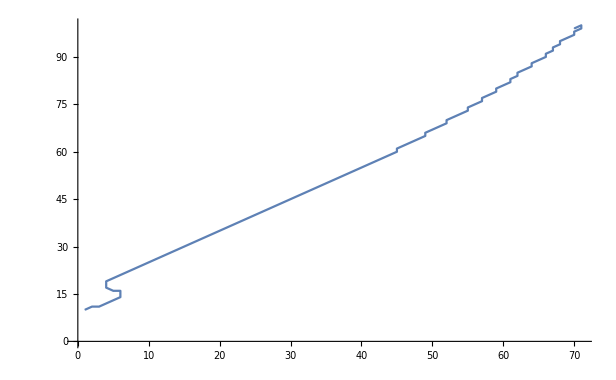

```mathematica
ListPlot[Reverse[points,2],PlotMarkers->{Automatic,1},Joined->True]
```

```mathematica
(*Search with bisection method until given precision*)
accuratePoints={};
p2s={};
p1s={};
For[i=2,i< Length[points],i++,
pt=points[[i]];
Δxy=points[[i+1]]-points[[i-1]];
pt1=points[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.7//N;
pt2=points[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.7//N;
μ1=μmin+(μmax-μmin)/(Nμ-1)*(pt1[[1]]-1);
If[μ1<1,μ1=1;pt1[[1]]=(μ1-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]]-1)/(Nγp-1));
μ2=μmin+(μmax-μmin)/(Nμ-1)*(pt2[[1]]-1);
If[μ2<1,μ2=1;pt2[[1]]=(μ2-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]]-1)/(Nγp-1));
res=result[[pt[[1]],pt[[2]]]];
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];

If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
For[k=1,k≤ 30&&res1==res&&res2==res,k++,
pt1=points[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1*k//N;
μ1=μmin+(μmax-μmin)/(Nμ-1)*(pt1[[1]]-1);
If[μ1<1,μ1=1;pt1[[1]]=(μ1-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]]-1)/(Nγp-1));
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
pt2=points[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1*k//N;
μ2=μmin+(μmax-μmin)/(Nμ-1)*(pt2[[1]]-1);
If[μ2<1,μ2=1;pt2[[1]]=(μ2-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]]-1)/(Nγp-1));
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
];
If[res==res1,pt1=pt,pt2=pt;];
];

(*If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
pt1=points[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*2//N;
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]+1);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]]+1)/Nγp);
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
pt2=points[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*2//N;
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]+1);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]]+1)/Nγp);
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
];*)
If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
Print["All points for binary search are still in one domain"];
Print[pt],];

p1s=Append[p1s,pt1];
p2s=Append[p2s,pt2];
If[res==res2,res2=res;pt2=pt,res1=res;pt1=pt];
While[Norm[pt1-pt2]>accuracy,
ptmid=(pt1+pt2)/2;
μmid=μmin+(μmax-μmin)/(Nμ-1)*(ptmid[[1]]-1);
If[μmid<1,μmid=1;ptmid[[1]]=(μmid-μmin)/(μmax-μmin)*(Nμ-1)+1];
γpmid=γpmin*(γpmax/γpmin)^((ptmid[[2]]-1)/(Nγp-1));
resmid=CheckStability[κ,α,γ,γd,γpmid,γa,μmid,Qp0,Qm0,a0][[1]];
If[resmid==res2,pt2=ptmid,pt1=ptmid];
];
accuratePoints=Append[accuratePoints,(pt1+pt2)/2];

];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

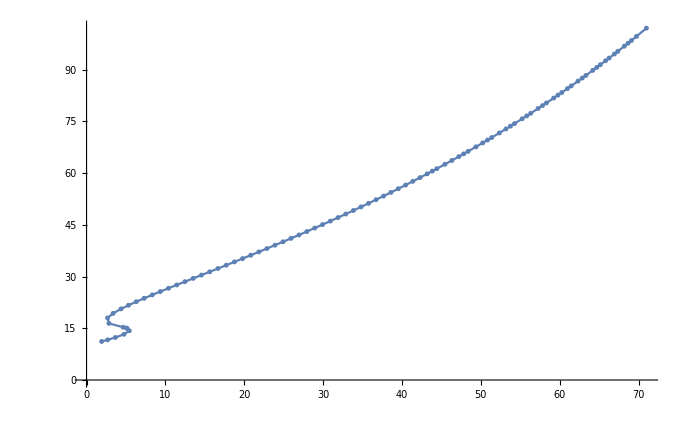

```mathematica
ListPlot[Reverse[accuratePoints,2],PlotMarkers->{Automatic,5},Joined->True]
```

```mathematica
toReassamble=accuratePoints;
k=0;
For[i=1,i< Length[toReassamble]&&k<300,i++,
k=k+1;
pt=toReassamble[[i]];
pt1=toReassamble[[i-1]];
pt2=toReassamble[[i+1]];
If[(pt-pt1).(pt2-pt)/Norm[(pt-pt1)]/Norm[pt2-pt]<-0.3,
placed=False;
j=i-1;
While[Not[placed],
ptp=toReassamble[[j]];
ptp2=toReassamble[[j+1]];
If[(ptp2-ptp).(pt2-ptp)/Norm[(ptp2-ptp)]/Norm[pt2-ptp]>-0.3,
Print["point placed ", j+1];
placed=True;
toReassamble=Delete[toReassamble,i+1];
toReassamble=Insert[toReassamble,pt2,j+1];
];
j=j-1;
];
i=i-1;
];
];
accuratePoints=toReassamble;
```

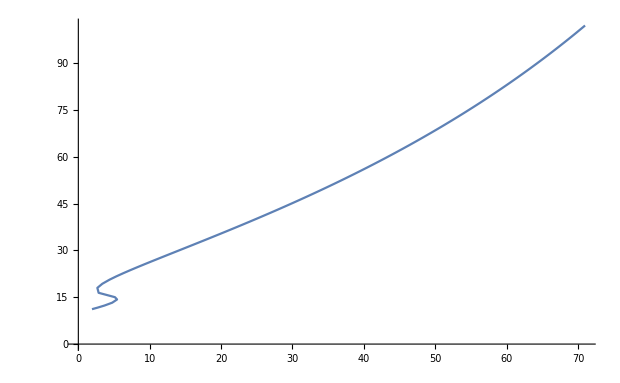

```mathematica
ListPlot[Reverse[toReassamble,2],Joined->True]
```

```mathematica
(*Interpolating fine boundary*)
PointNum=500;
sums=Prepend[Table[Sum[Norm[accuratePoints[[i]]-accuratePoints[[i-1]]],{i,2,j}],{j,2,Length[accuratePoints]}],0];
interp=Interpolation[Transpose[{sums,accuratePoints}],Method->"Spline"];
initfinepts=Table[interp[Last[sums]/(PointNum)*i],{i,0,PointNum}];
```

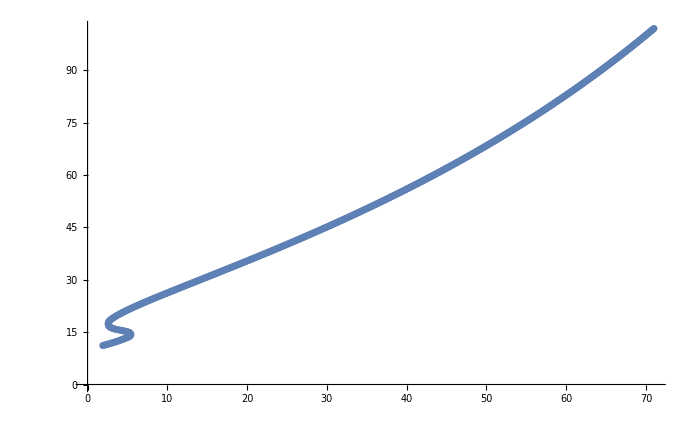

```mathematica
ListPlot[Reverse[initfinepts,2]]
```

```mathematica
(*Additional fine boundary search*)
finepts={};
p1s={};
p2s={};
For[i=2,i< Length[initfinepts],i++,
pt=initfinepts[[i]];
Δxy=initfinepts[[i+1]]-initfinepts[[i-1]];
pt1=initfinepts[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.5//N;
pt2=initfinepts[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.5//N;
μ=μmin+(μmax-μmin)/(Nμ-1)*(pt[[1]]-1);
γp=γpmin*(γpmax/γpmin)^((pt[[2]])/Nγp);
If[μ<1,μ=1;pt[[1]]=(μ-μmin)/(μmax-μmin)*(Nμ-1)+1];

μ1=μmin+(μmax-μmin)/(Nμ-1)*(pt1[[1]]-1);
If[μ1<1,μ1=1;pt1[[1]]=(μ1-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]]-1)/(Nγp-1));

μ2=μmin+(μmax-μmin)/(Nμ-1)*(pt2[[1]]-1);
If[μ2<1,μ2=1;pt2[[1]]=(μ2-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]]-1)/(Nγp-1));

res=CheckStability[κ,α,γ,γd,γp,γa,μ,Qp0,Qm0,a0][[1]];
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];

If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],For[k=1,k≤15&&res1==res&&res2==res,k++,pt1=initfinepts[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1*k//N;
μ1=μmin+(μmax-μmin)/(Nμ-1)*(pt1[[1]]-1);
If[μ1<1,μ1=1;pt1[[1]]=(μ1-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]]-1)/(Nγp-1));
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
pt2=initfinepts[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1*k//N;
μ2=μmin+(μmax-μmin)/(Nμ-1)*(pt2[[1]]-1);
If[μ2<1,μ2=1;pt2[[1]]=(μ2-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]]-1)/(Nγp-1));
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];];
If[res==res1,pt1=pt,pt2=pt;];];

(*If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
For[k=2,k≤ 10&&res1==res,k++,
pt1=initfinepts[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.2*k//N;
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]])/Nγp);
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
];
If[res==res1,pt1=pt;
For[k=2,k≤ 10&&res2==res,k++,
pt2=initfinepts[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.2*k//N;
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]])/Nγp);
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
],pt2=pt;];

];*)
If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
Print["All points for binary search are still in one domain. Ignoring point:"];
Print[i];
Print[pt];
Print[{pt1,pt2}],

p1s=Append[p1s,pt1];
p2s=Append[p2s,pt2];
If[res1+res==1,res2=res;pt2=pt,res1=res;pt1=pt];
While[Norm[pt1-pt2]>accuracy,
ptmid=(pt1+pt2)/2;
μmid=μmin+(μmax-μmin)/(Nμ-1)*(ptmid[[1]]-1);
If[μmid<1,μmid=1;ptmid[[1]]=(μmid-μmin)/(μmax-μmin)*(Nμ-1)+1];
γpmid=γpmin*(γpmax/γpmin)^((ptmid[[2]]-1)/(Nγp-1));
resmid=CheckStability[κ,α,γ,γd,γpmid,γa,μmid,Qp0,Qm0,a0][[1]];
If[resmid==res2,pt2=ptmid,pt1=ptmid];
];
finepts=Append[finepts,(pt1+pt2)/2];
];
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

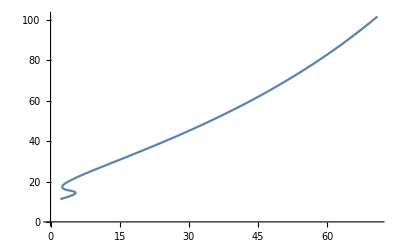

```mathematica
ListPlot[Reverse[finepts,2],Joined->True]
```

```mathematica
toReassamble=finepts;
k=0;
For[i=1,i< Length[toReassamble]&&k<300,i++,
k=k+1;
pt=toReassamble[[i]];
pt1=toReassamble[[i-1]];
pt2=toReassamble[[i+1]];
If[(pt-pt1).(pt2-pt)/Norm[(pt-pt1)]/Norm[pt2-pt]<-0.1,
placed=False;
j=i-1;
While[Not[placed],
ptp=toReassamble[[j]];
ptp2=toReassamble[[j+1]];
If[(ptp2-ptp).(pt2-ptp)/Norm[(ptp2-ptp)]/Norm[pt2-ptp]>-0.1,
Print["point placed ", j+1];
placed=True;
toReassamble=Delete[toReassamble,i+1];
toReassamble=Insert[toReassamble,pt2,j+1];
];
j=j-1;
];
i=i-1;
];
];
finepts=toReassamble;
```

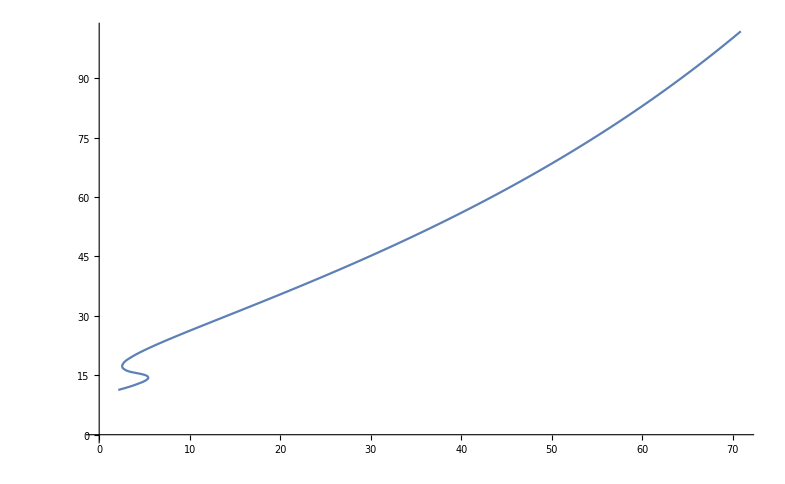

```mathematica
ListPlot[Reverse[finepts,2],Joined->True]
```

```mathematica
(*Additional smoothing*)
PointNum2=1000;
accuracy2=10^-7;
sums2=Prepend[Table[Sum[Norm[finepts[[i]]-finepts[[i-1]]],{i,2,j}],{j,2,Length[finepts]}],0];
interp2=Interpolation[Transpose[{sums2,finepts}],Method->"Spline"];
initfinepts2=Table[interp2[Last[sums2]/(PointNum2)*i],{i,0,PointNum2}];
finepts2={};
p1s={};
p2s={};
For[i=2,i< Length[initfinepts2],i++,
pt=initfinepts2[[i]];
Δxy=initfinepts2[[i+1]]-initfinepts2[[i-1]];
pt1=initfinepts2[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1//N;
pt2=initfinepts2[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.1//N;
μ=μmin+(μmax-μmin)/(Nμ-1)*(pt[[1]]-1);
If[μ<1,μ=1;pt[[1]]=(μ-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp=γpmin*(γpmax/γpmin)^((pt[[2]]-1)/(Nγp-1));
μ1=μmin+(μmax-μmin)/(Nμ-1)*(pt1[[1]]-1);
If[μ1<1,μ1=1;pt1[[1]]=(μ1-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]]-1)/(Nγp-1));
μ2=μmin+(μmax-μmin)/(Nμ-1)*(pt2[[1]]-1);
If[μ2<1,μ2=1;pt2[[1]]=(μ2-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]]-1)/(Nγp-1));
res=CheckStability[κ,α,γ,γd,γp,γa,μ,Qp0,Qm0,a0][[1]];
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];

If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
For[k=1,k≤ 10&&res1==res&&res2==res,k++,
pt1=initfinepts2[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.03*k//N;
μ1=μmin+(μmax-μmin)/(Nμ-1)*(pt1[[1]]-1);
If[μ1<1,μ1=1;pt1[[1]]=(μ1-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]]-1)/(Nγp-1));
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
pt2=initfinepts2[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.03*k//N;
μ2=μmin+(μmax-μmin)/(Nμ-1)*(pt2[[1]]-1);
If[μ2<1,μ2=1;pt2[[1]]=(μ2-μmin)/(μmax-μmin)*(Nμ-1)+1;];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]]-1)/(Nγp-1));
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
];
If[res==res1,pt1=pt,pt2=pt;];
];

(*If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
For[k=3,k≤ 10&&res1==res,k++,
pt1=initfinepts2[[i]]+{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.005*k//N;
μ1=μmin+(μmax-μmin)/Nμ*(pt1[[1]]);
If[μ1<1,μ1=1];
γp1=γpmin*(γpmax/γpmin)^((pt1[[2]])/Nγp);
res1=CheckStability[κ,α,γ,γd,γp1,γa,μ1,Qp0,Qm0,a0][[1]];
];
If[res==res1,pt1=pt;
For[k=3,k≤ 10&&res2==res,k++,
pt2=initfinepts2[[i]]-{Δxy[[2]],-Δxy[[1]]}/Sqrt[Δxy[[1]]^2+Δxy[[2]]^2]*0.005*k//N;
μ2=μmin+(μmax-μmin)/Nμ*(pt2[[1]]);
If[μ2<1,μ2=1];
γp2=γpmin*(γpmax/γpmin)^((pt2[[2]])/Nγp);
res2=CheckStability[κ,α,γ,γd,γp2,γa,μ2,Qp0,Qm0,a0][[1]];
],pt2=pt;];

];*)
If[AllTrue[{res,res1,res2},#==0&]||AllTrue[{res,res1,res2},#==1&],
Print["All points for binary search are still in one domain. Ignoring point:"];
Print[i];
Print[pt];
Print[{pt1,pt2}],

p1s=Append[p1s,pt1];
p2s=Append[p2s,pt2];
If[res1+res==1,res2=res;pt2=pt,res1=res;pt1=pt];
While[Norm[pt1-pt2]>accuracy2,
ptmid=(pt1+pt2)/2;
μmid=μmin+(μmax-μmin)/(Nμ-1)*(ptmid[[1]]-1);
If[μmid<1,μmid=1;ptmid[[1]]=(μmid-μmin)/(μmax-μmin)*(Nμ-1)+1];
γpmid=γpmin*(γpmax/γpmin)^((ptmid[[2]]-1)/(Nγp-1));
resmid=CheckStability[κ,α,γ,γd,γpmid,γa,μmid,Qp0,Qm0,a0][[1]];
If[resmid==res2,pt2=ptmid,pt1=ptmid];
];
finepts2=Append[finepts2,(pt1+pt2)/2];
];
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
(*Evaluating real boundary in terms of γp and μ*)
initboundary=Table[{μmin+(μmax-μmin)/(Nμ-1)*(finepts2[[i,1]]-1),γpmin*(γpmax/γpmin)^((finepts2[[i,2]]-1)/(Nγp-1))},{i,1,Length[finepts2]}];
boundaryScaled=Table[{initboundary[[i,1]]*(1-Ntr/Nth)+Ntr/Nth,initboundary[[i,2]]/(2π)},{i,1,Length[initboundary]}];
```

```mathematica
SetDirectory["D:\\work\\VCSEL experiments\\TeXи\\graphs"];
boundaryAdd=Reverse[boundaryScaled,2];
Save["fig[k_a_gd][300 500 5].m",{boundaryAdd}]
```

```mathematica
boundary={boundary,boundaryAdd}//Flatten[#,1]&;
```

```mathematica
Save["fig[k_a_gd][300 200 5]--merged.m",{γa,γ,γd,κ,α,Nth,Ntr,boundary}]
```

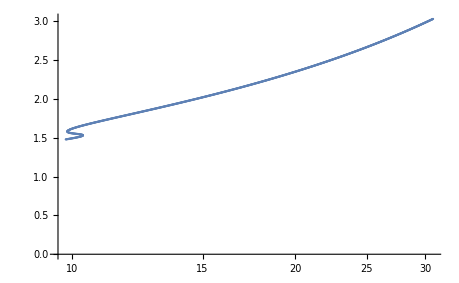

```mathematica
ListLinePlot[Reverse[boundaryScaled,2],ScalingFunctions->{"Log10",None},PlotMarkers->{Automatic,2}]
```

```mathematica
Import[]
```

```mathematica
{First[boundaryScaled][[2]],Last[boundaryScaled][[2]]}
```

{0.20382,3.88865}

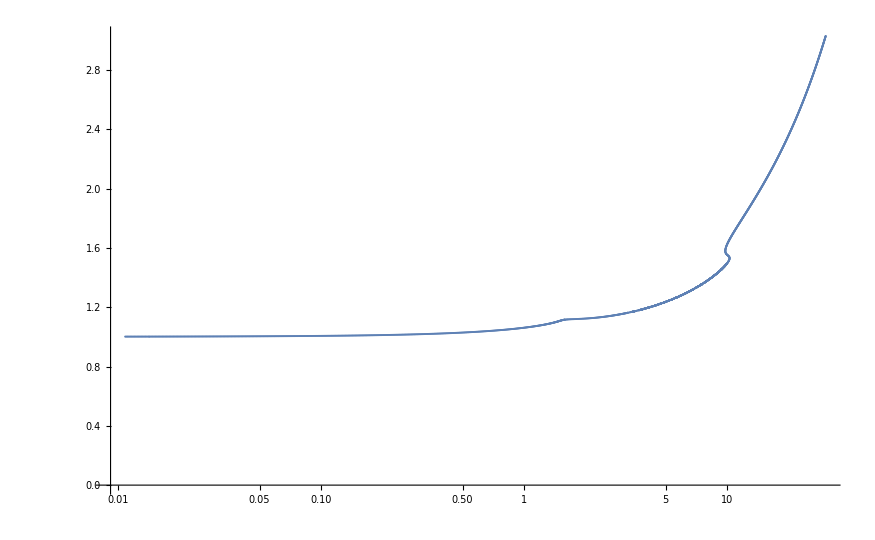

```mathematica
ListPlot[boundary,ScalingFunctions->{"Log10",None},PlotMarkers->{Automatic,2}]
```

```mathematica
boundaryScaled[[1]]
```

{1.49463,10.4139}

```mathematica
boundaryScaled[[1]]//Last
```

0.307904

```mathematica
llp=ListLinePlot[Reverse[finepts2,2],PlotMarkers->{Automatic,2},PlotStyle->{Thick,Orange}]
```

```mathematica
FindPath[NearestNeighborGraph[finepts2],First[finepts2],Last[finepts2]]
```

{}

```mathematica
finepts3=finepts2[[Last[FindShortestTour[finepts2,1,Length[finepts2]]]]];
```

```mathematica
finepts=finepts3;
```

```mathematica
boundary=Reverse[boundaryScaled[[Last[FindShortestTour[boundaryScaled,1,Length[boundaryScaled]]]]],2];
```

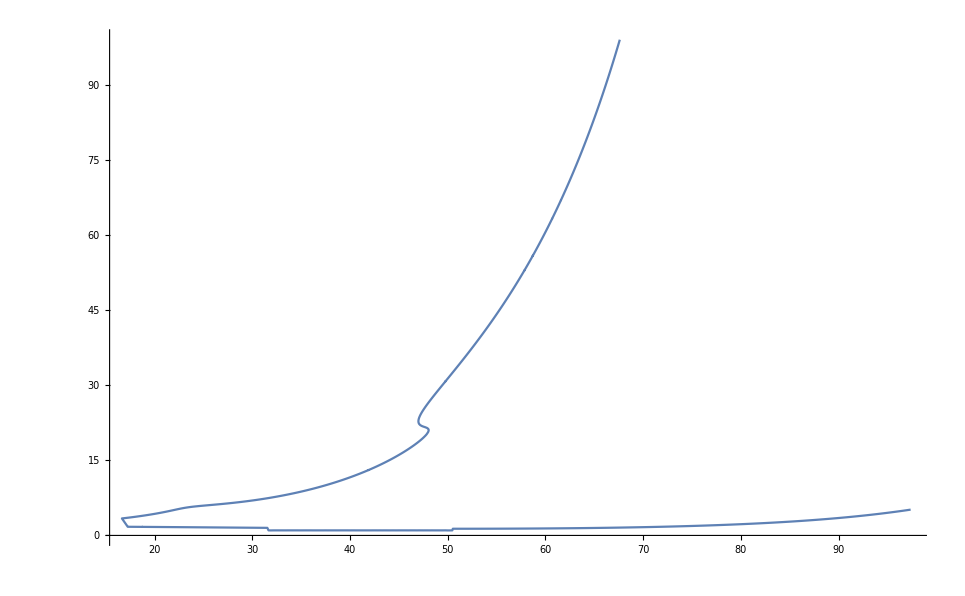

```mathematica
ListPlot[Reverse[finepts3,2],Joined->True]
```

```mathematica
{Last[boundaryScaled][[1]],Last[boundaryScaled][[2]]/(2π)}
```

{1.09879,1.00886}

```mathematica
ClearAll["Global`*"];
SetDirectory["D:\\work\\VCSEL experiments\\TeXи\\graphs"];
```

```mathematica
SetDirectory["D:\\work\\VCSEL experiments\\TeXи\\graphs"];
Import["fig[k_a_gd][300 200 5].m"];
```

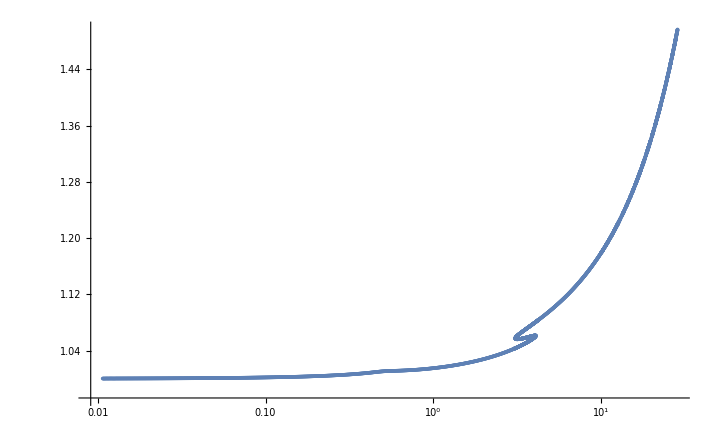

```mathematica
ListPlot[boundary,ScalingFunctions->{"Log10",None}]
```

```mathematica
initpoints={boundaryP1,boundaryP2,boundaryP3}//Flatten[#,1]&;
PointNum3=2000;
accuracy3=10^-7;
sums3=Prepend[Table[Sum[Norm[initpoints[[i]]-initpoints[[i-1]]],{i,2,j}],{j,2,Length[initpoints]}],0];
interp3=Interpolation[Transpose[{sums3,initpoints}],Method->"Spline"];
initfinepts3=Table[interp3[Last[sums3]/(PointNum3)*i],{i,0,PointNum3}];
```

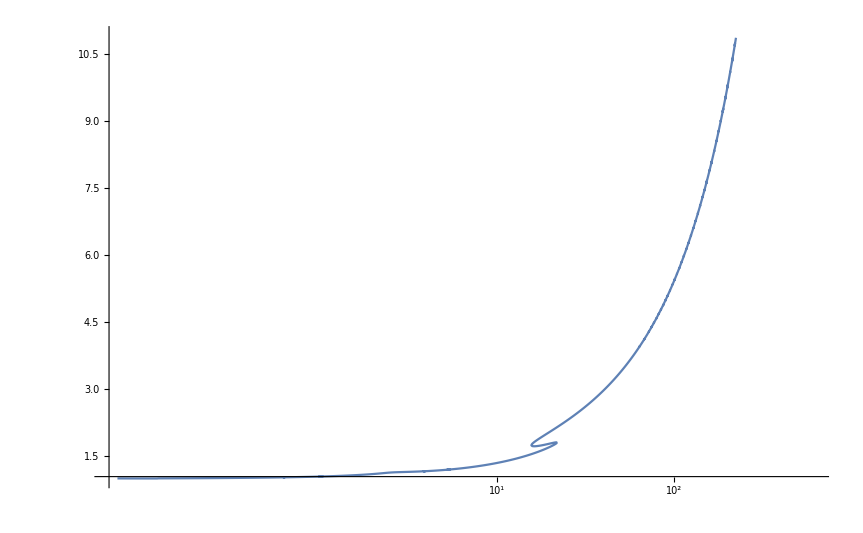

```mathematica
(*Plotting boundary*)
ListPlot[Reverse[boundary,2],Joined-> True,ScalingFunctions->{"Log10",None},PlotRange->{{γpmin,γpmax},{μmin,μmax}}]
```

### Plotting by pixels v2

```mathematica
γa=-0.01;
γ=1.;
γp=-10;
κ=300.;
γd=50.;
α=3.;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;
Nμ=100;
Nγp=100;
μs=CoordinateBoundsArray[{{1.,6.}},Into[Nμ]]//Flatten;
γps=CoordinateBoundsArray[{{1.,2.}},Into[Nγp]]//Flatten//Power[10,#]&;
result=ConstantArray[0,{Nγp,Nμ}];
For[i=1,i<= Nμ,i++,
For[j=1,j<= Nγp,j++,
μ=μs[[i]];
γp=γps[[j]];
Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
Nsol=Flatten[{Nsol,ψ-> ArcSin[a/.Nsol]/2}];

p=-CoefficientList[CharacteristicPolynomial[(tmp3/.{Λ-> μ}/.Nsol),λ],λ];

If[AllTrue[p,Positive],
Dets=ConstantArray[0,2];
Dets[[1]]=p[[4]]*p[[5]]-p[[3]]; (*D2*)
Dets[[2]]=Det[{
{p[[5]],p[[3]],p[[1]],0},
{1,p[[4]],p[[2]],0},
{0,p[[5]],p[[3]],p[[1]]},
{0,1,p[[4]],p[[2]]}}];(*D4*)

If[AllTrue[Dets,Positive],
result[[i,j]]=0;
If[Dets[[1]]>0,result[[i,j]]=0.3,];
If[Dets[[2]]>0,result[[i,j]]=result[[i,j]]+0.7,] 
,
result[[i,j]]=0
],
If[oldresult[[i,j]]>0,Print[i," ",j],]
]
]];
Image[Reverse[result]]
```

Power::infy: Infinite expression 1/0. encountered.

CharacteristicPolynomial::inf: Input matrix contains an infinite entry.

Power::infy: Infinite expression 1/0. encountered.

CharacteristicPolynomial::inf: Input matrix contains an infinite entry.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

CharacteristicPolynomial::inf: Input matrix contains an infinite entry.

General::stop: Further output of CharacteristicPolynomial::inf will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {0.107997,0.906551,1.} is at the edge of the search region {1.×10^-8,10.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.123634,0.910422,1.} is at the edge of the search region {1.×10^-8,10.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.139076,0.914214,1.} is at the edge of the search region {1.×10^-8,10.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

-Graphics-

```mathematica
Image[Reverse[oldresult-result]]
Image[Reverse[oldresult]]
```

-Graphics-

-Graphics-

```mathematica
μ=μs[[100]];
γp=γps[[83]];
Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
Nsol=Flatten[{Nsol,ψ-> ArcSin[a/.Nsol]/2}];
p=charpolycoefs/.Nsol;
Dets=ConstantArray[0,2];
Dets[[1]]=p[[4]]*p[[5]]-p[[3]]; (*D2*)
Dets[[2]]=Det[{
{p[[5]],p[[3]],p[[1]],0},
{1,p[[4]],p[[2]],0},
{0,p[[5]],p[[3]],p[[1]]},
{0,1,p[[4]],p[[2]]}}];(*D4*)
```

```mathematica
p
```

{1.02348×10^10,1.18555×10^8,-1.30236×10^6,35269.8,121.689}